### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={100,500,500}; (*мощности слоев*)
slopes = {0Degree, -0.9 Degree, -0.3 Degree, 2 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = 1 ;
listV = {1500,2000,2300,2500, 2800}; (*набор скоростей *)
```

```mathematica
(*folding parametres *)
hDispersion = 300;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
velocityTrend = {0,1,1,1,1};(*1 or 0*)
velocityAnomaly ={1,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
(*PlotVelocity[velModel, horizons]*)
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[-17.6769+3367.01 t],FittedModel[-30.1133+3766.18 t],FittedModel[133.165+3496.25 t],FittedModel[635.405+2580.95 t]}

{{{0.0592786,187.173},{0.0641131,203.173},{0.0666372,213.173},{0.0671459,215.173},{0.0673797,215.173},{0.0649127,190.173},{0.0254347,67.1728},{0.03097,91.1728},{0.0573485,164.173},{0.0621171,180.173}},{{0.136702,489.173},{0.143617,511.173},{0.14973,537.173},{0.150623,542.173},{0.148075,536.173},{0.115678,385.173},{0.0491263,160.173},{0.0808289,292.173},{0.0995255,332.173},{0.107627,363.173}},{{0.268428,1066.17},{0.274621,1069.17},{0.281765,1113.17},{0.285973,1131.17},{0.290514,1170.17},{0.239166,920.173},{0.180719,755.173},{0.225945,967.173},{0.237271,970.173},{0.25005,1030.17}},{{0.471984,1862.17},{0.445106,1766.17},{0.484913,1894.17},{0.487794,1903.17},{0.534885,2027.17},{0.41767,1676.17},{0.397866,1675.17},{0.518522,2009.17},{0.520902,1993.17},{0.585117,2103.17}}}

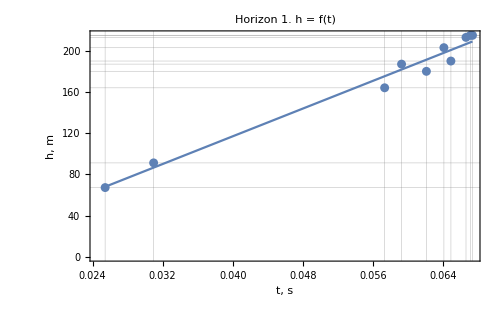
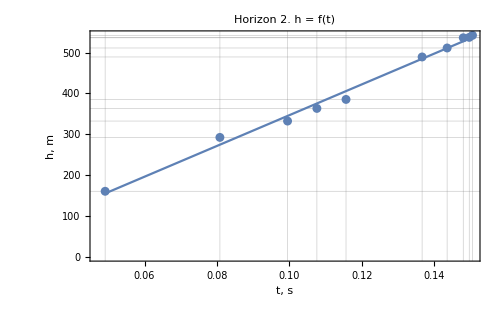
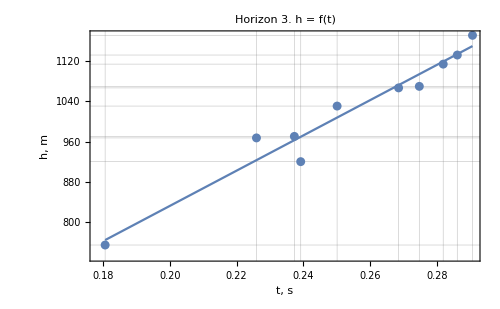
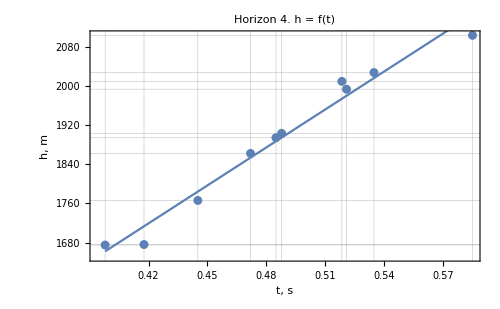

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]]
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[2504.53+9120.13 t],FittedModel[3155.02+2803.41 t],FittedModel[4635.77-2384.3 t],FittedModel[5213.56-2693.93 t]}

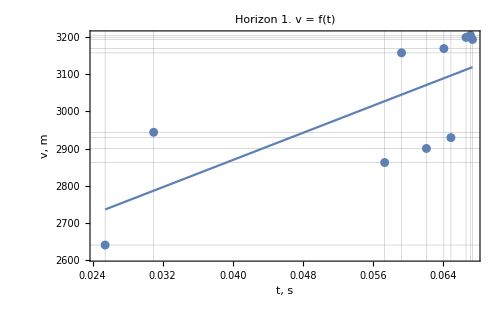
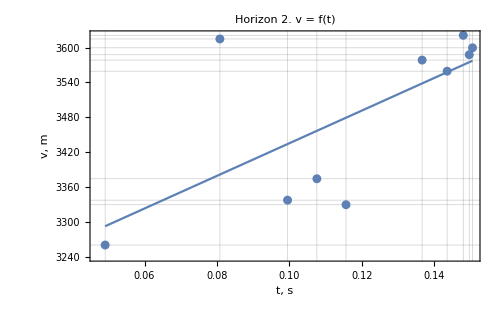
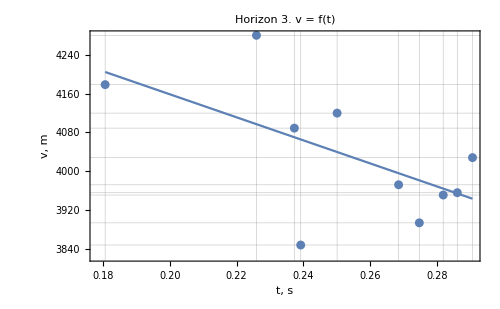
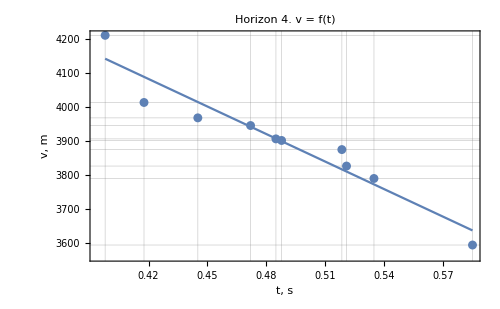

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[0.00643084+0.000290161 h],FittedModel[0.00886796+0.000263419 h],FittedModel[-0.0247235+0.000272909 h],FittedModel[-0.225982+0.000376768 h]}

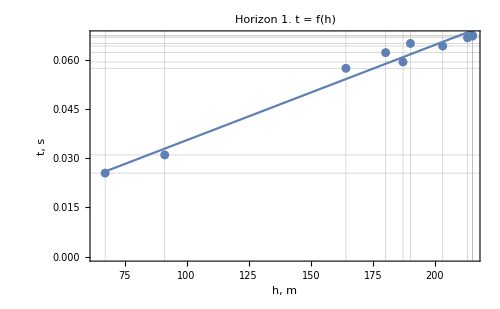
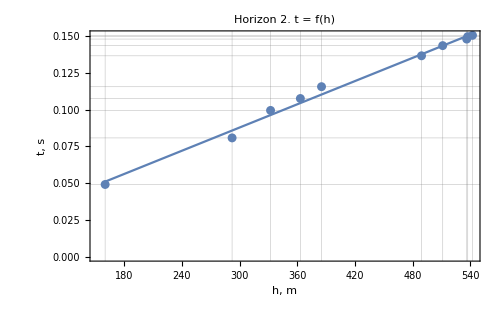
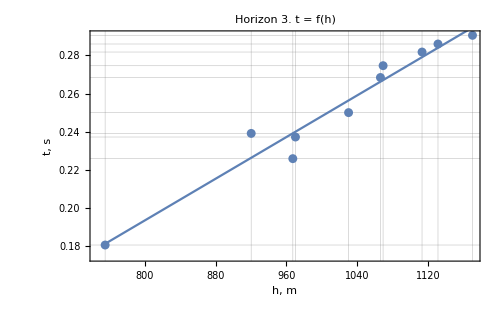
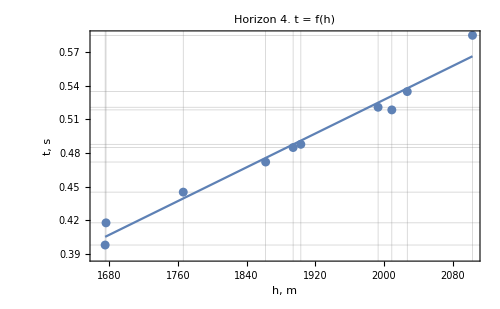

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]];
```

{3020.13,3486.25,4031.48,3903.03}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-